# Diplomado en programación básica // MCTP 2023

Luis Gerardo Ramirez Archundia

08/02/2023

Evalúe cada una de las expresiones algebraicas, dado que x=-1, y =3, z=2, a=1/2, b=-2/3.

```mathematica
4x^3y^2-3x z^2/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-24

```mathematica
(x-y) (y-z)(z-x)/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-12

```mathematica
9 a b^2+6 a b-4  a^2/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-1

```mathematica
(x y^2-3z)/(a+b)/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

90

```mathematica
(z (x+y))/(8 a^2)-(3 a b)/(y-x)/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

9/4

```mathematica
((x-y)^2+2 z)/(a x+b y)/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-8

```mathematica
1/x+1/y+1/z/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-1/6

```mathematica
((x-1)(y-1)(z-1))/((a-1)(b-1))/.{x->-1,y->3,z->2,a->1/2,b->-2/3}
```

-24/5

Desarrollar

```mathematica
2 x y (3x^2 y-4y^3)//Expand
```

6 x^3 y^2-8 x y^4

```mathematica
3x^2y^3(2x y-x-2y)//Expand
```

-3 x^3 y^3-6 x^2 y^4+6 x^3 y^4

```mathematica
(2s t^3-4r s^2+3s^3 t)(5r s t^2)//Expand
```

-20 r^2 s^3 t^2+15 r s^4 t^3+10 r s^2 t^5

```mathematica
(3a+5b)(3a-5b)//Expand
```

9 a^2-25 b^2

```mathematica
(5 x y+4)(5 x y-4 )//Expand
```

-16+25 x^2 y^2

```mathematica
(2-5y^2)(2+5y^2)//Expand
```

4-25 y^4

```mathematica
(3a+5a^2b)(3a-5a^2b)//Expand
```

9 a^2-25 a^4 b^2

```mathematica
(x+6)^2//Expand
```

36+12 x+x^2

```mathematica
(y+3x)^2//Expand
```

9 x^2+6 x y+y^2

```mathematica
(z-4)^2//Expand
```

16-8 z+z^2

```mathematica
(3-2x^2)^2//Expand
```

9-12 x^2+4 x^4

```mathematica
(x^2y-2z)^2//Expand
```

x^4 y^2-4 x^2 y z+4 z^2

```mathematica
(x+2)(x+4)//Expand
```

8+6 x+x^2

Factoriza

```mathematica
3x^2y^4+6x^3y^3//FullSimplify
```

3 x^2 y^3 (2 x+y)

```mathematica
12 s^2t^2-6s^5t^4+4s^4t//FullSimplify
```

2 s^2 t (6 t+s^2 (2-3 s t^3))

```mathematica
2x^2y z-4x y z^2+8x y^2 z^3//FullSimplify
```

2 x y z (x+2 z (-1+2 y z))

```mathematica
4 y^2-100//FullSimplify
```

4 (-25+y^2)

```mathematica
1-a^4//FullSimplify
```

1-a^4

```mathematica
64x-x^3//FullSimplify
```

-x (-64+x^2)

```mathematica
8x^4-128//FullSimplify
```

8 (-16+x^4)

```mathematica
18x^3y-8xy^3//FullSimplify
```

-8 xy^3+18 x^3 y

```mathematica
(2x+y)^2-(3y-z)^2//FullSimplify
```

(2 x+y)^2-(-3 y+z)^2

```mathematica
4(x+3 y)^2-9(2 x-y)^2//FullSimplify
```

-((4 x-9 y) (8 x+3 y))

```mathematica
x^2+4x+4//FullSimplify
```

(2+x)^2

```mathematica
x^2y^2-8x y+16//FullSimplify
```

(-4+x y)^2

```mathematica
4 x^3 y+12x^2 y^2+9x  y^3//FullSimplify
```

x y (2 x+3 y)^2

```mathematica
3 a^4+6 a^2 b^2+3 b^4//FullSimplify
```

3 (a^2+b^2)^2

```mathematica
(m^2-n^2)^2+8(m^2-n^2)+16//FullSimplify
```

(4+m^2-n^2)^2

```mathematica
x^2+7 x+12//FullSimplify
```

(3+x) (4+x)

```mathematica
y^2-4 y-5//FullSimplify
```

(-5+y) (1+y)

```mathematica
x^2-8x y+15y^2//FullSimplify
```

(x-5 y) (x-3 y)

```mathematica
2z^3+10z^2-28z//FullSimplify
```

2 (-2+z) z (7+z)

```mathematica
15+2x-x^2//FullSimplify
```

-((-5+x) (3+x))

Encontrar al menos una raíz de las siguientes funciones trigonométricas

3.14159

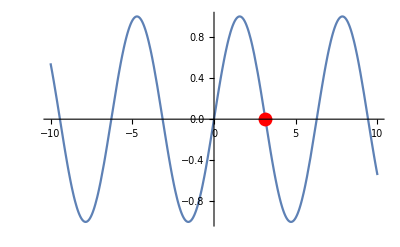

```mathematica
f[x_]=Sin[x];
raiz=x/.FindRoot[f[x],{x,3}]
grafica=Plot[f[x],{x,-10,10}, PlotRange->All];
punto=Graphics[{PointSize[0.025],Red,Point[{raiz,0}]}];
Show[grafica,punto]
```

-4.71239

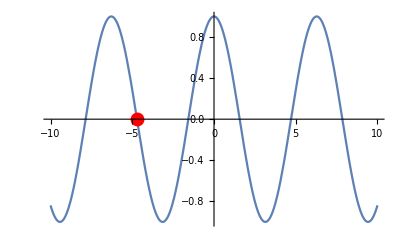

```mathematica
f[x_]=Cos[x];
raiz=x/.FindRoot[f[x],{x,3}]
grafica=Plot[f[x],{x,-10,10}, PlotRange->All];
punto=Graphics[{PointSize[0.025],Red,Point[{raiz,0}]}];
Show[grafica,punto]
```

0.

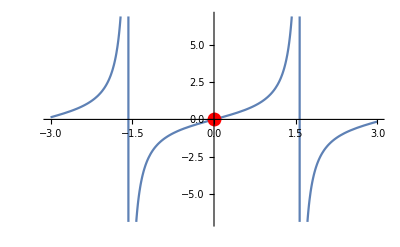

```mathematica
f[x_]=Tan[x];
raiz=x/.FindRoot[f[x],{x,0}]
grafica=Plot[f[x],{x,-3,3}, PlotRange->Automatic];
punto=Graphics[{PointSize[0.025],Red,Point[{raiz,0}]}];
Show[grafica,punto]
```

1.5708

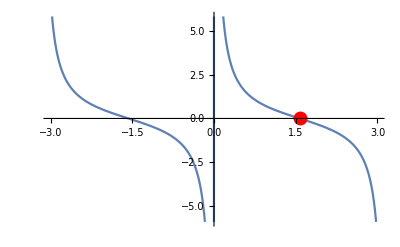

```mathematica
f[x_]=Cot[x];
raiz=x/.FindRoot[f[x],{x,2}]
grafica=Plot[f[x],{x,-3,3}, PlotRange->Automatic];
punto=Graphics[{PointSize[0.025],Red,Point[{raiz,0}]}];
Show[grafica,punto]
```

Las funciones Secante y Cosecante no tienen raíces por definición.

Encontrar el valor de cada incógnita de las siguientes expresiones:

```mathematica
Solve[3x-2==7]
```

{{x→3}}

```mathematica
Solve[y+3 (y-4 )==4]
```

{{y→4}}

```mathematica
Solve[4 x-3==5-2 x]
```

{{x→4/3}}

```mathematica
Solve[x-3-2(6-2x)==2 (2x-5)]
```

{{x→5}}

```mathematica
Solve[(2 t-9)/3==(3 t+4)/2]
```

{{t→-6}}

```mathematica
Solve[(2 x+3)/(2 x-4)==(x-1)/(x+1)]
```

{{x→1/11}}

```mathematica
Solve[(x-3)^2+(x+1)^2==(x-2)^2+(x+3)^2]
```

{{x→-1/2}}

```mathematica
Solve[(2x+1)^2==(x-1)^2+3  x (x+2)]
```

{{}}

```mathematica
Solve[3/z-4/(5 z)==1/10]
```

{{z→22}}

```mathematica
Solve[(2 x+1)/x+(x-4)/(x+1)==3]
```

{{x→1/4}}

```mathematica
Solve[5/(y-1)-5/(y+1)==2/(y-2)-2/(y+3)]
```

{{y→5}}

```mathematica
Solve[7/(x^2-4)+2/(x^2-3x+2)==4/(x^2+x-2)]
```

{{x→-1}}

Resuelve los siguientes sistemas de ecuaciones:

```mathematica
Remove[solucion1,solucion2,y]
Solve[2x-5y==10&&4 x+3 y==7,{x,y}]
solucion1=y/.Solve[2x-5y==10];
solucion2=y/.Solve[4 x+3 y==7];
Plot[{solucion1,solucion2},{x,-10,10}, PlotLabels->Automatic]
```

{{x→5/2,y→-1}}

-Graphics-

```mathematica
Remove[solucion1,solucion2,y]
Solve[2 y-x==1&&2 x+y==8,{x,y}]
solucion1=y/.Solve[2 y-x==1];
solucion2=y/.Solve[2 x+y==8];
Plot[{solucion1,solucion2},{x,-10,10}, PlotLabels->Automatic]
```

{{x→3,y→2}}

-Graphics-

```mathematica
Remove[solucion1,solucion2,y]
Solve[2 x-3 y==9 &&4 x-y==8,{x,y}]
solucion1=y/.Solve[2 x-3 y==9];
solucion2=y/.Solve[4 x-y==8];
Plot[{solucion1,solucion2},{x,-10,10}, PlotLabels->Automatic]
```

{{x→3/2,y→-2}}

-Graphics-

```mathematica
Remove[solucion1,solucion2,y]
Solve[2 x+y+1==0&&3 x-2 y+5==0]
solucion1=y/.Solve[2 x+y+1==0];
solucion2=y/.Solve[3 x-2 y+5==0];
Plot[{solucion1,solucion2},{x,-10,10}, PlotLabels->Automatic]
```

{{x→-1,y→1}}

-Graphics-

En el ejercicio anterior graficar los sistemas de ecuaciones.